# Risk Plots

```mathematica
figurePath="~/work/papers/alpha-invest/optimal/figures/";
```

## Bellman solutions

Plots show a convex hull of the feasible set.  Some add traces of solutions for iid mean process (as in the iid spike-and-slab Bayesian model).

For each configuration run, the data that is read from C++ is structured as a list of 3 items
	file name
	parameter values (as alpha, beta, omega, scale and n)
	simulation results.
A nested list of parameter values is given for the row (oracle) and column (statistician) players, followed by the universal scale (which may not be relevant) and the length of the test sequence.  For each player, the list includes the initial wealth W_0, the probability parameter, and the payout ω.  The probability parameter identifies the alpha-investing method, as defined below.

Transfer file from server.  Parsing of parameter values, with special cases... 
	alpha = defines oracle		 					0 mins LS risk, and 1 mins risk, and other mins testimator risk
	beta = rate used by bidder if geometric				0 for universal (if omega=0, then bid = beta/n)
	omega = payout for each player					0 indicates fixed bid (ie, old fashioned), 1 means unconstrained
	scale = scale parameter of universal distribution			Not relevant in final version

### Functions for plotting and reading data ...

Idea is to make a file name based on parameter values.  Keep the file name and list of parameter values as the first two items in a list with the data last.

#### data functions, get

```mathematica
Clear[fmt,makeID,  getAlpha, getBeta,getOmegaAlpha,getOmegaBeta, getW0Alpha, getW0Beta,getN, getData];

fmt[0]="00";

fmt[x_/;x<.001]:=With[{s= ToString[Round[10000x]]},
If[StringLength[s]>1,s,StringJoin["000",s]]
]
fmt[x_/;x<.01]:=With[{s= ToString[Round[1000x]]},
If[StringLength[s]>1,s,StringJoin["00",s]]
]

fmt[x_]:=With[{s= ToString[Round[100x]]},
If[StringLength[s]>1,s,StringJoin["0",s]]
]

makeID[{W0α_,α_,ωα_},{W0β_,β_,ωβ_}, scale_, n_] :=
{StringJoin["summary_risk",
"_alpha",fmt[W0α],"_",fmt[α],"_",fmt[ωα],
"_beta"  ,fmt[W0β],"_",fmt[β],"_",fmt[ωβ] ,
"_scale",ToString[scale],"_n",ToString[n]],
{{W0α,α,ωα},{W0β,β,ωβ},scale,n}
}

getAlpha[{_,parms_,_}] :=getAlpha[parms]
getAlpha[{{_,α_,_},_List,_,_}] :=α

getBeta[{_,parms_,_}] :=getBeta[parms]
getBeta[{_List,{_,β_,_},_,_}] :=β

getOmega[{_,parms_,_}] :=getOmega[parms]
getOmega[{_List,{_,_,ω_},_,_}] :=ω

getAlphaBeta[{_,parms_,_}] :=getAlphaBeta[parms]
getAlphaBeta[{{_,α_,_},{_,β_,_},_,_}] :={α,β}

getOmegaAlpha[{_,parms_,_}]:=getOmegaAlpha[parms]
getOmegaAlpha[{{_,_,ω_},_List,_,_}]:=ω

getOmegaBeta[{_,parms_,_}]:=getOmegaBeta[parms]
getOmegaBeta[{_List,{_,_,ω_},_,_}]:=ω

getW0Alpha[{_,parms_,_}]:=getW0Alpha[parms]
getW0Alpha[{{W0_,_,_},_List,_,_}]:=W0

getW0Beta[{_,parms_,_}]:=getW0Beta[parms]
getW0Beta[{_List,{W0_,_,_},_,_}]:=W0

getW0Omega[{_,parms_,_}] :=getW0Omega[parms]
getW0Omega[{_,{w0_,_,ω_},_,_}] :={w0,ω}

getN[{_,parms_,_}] :=getN[parms]
getN[{_List,_List,_,n_}] :=n


getData[{name_,parms_},figureNumber_,server_]:=Module[
{fN=ToString[figureNumber],
path=StringJoin["~/C/bellman/figures/f",ToString[figureNumber],"/"],
fullName,x, cmd},
fullName=StringJoin[path,name];
If[StringLength[server]>1,
cmd = StringJoin["scp ",server,fullName," ", path];
(* Print["Getting file from server; command is ", cmd]; *)
Run[cmd]];
x= Import[fullName, "Table"];
If[x===$Failed,
Print[name," read failed."];{name,parms,Null},
{name,parms,Sort[x,#1⟦1⟧<#2⟦1⟧&]} (* sort on angle *)
]]
```

#### pick columns, players

The function pickColumns adds 1 to the risk (as for implicitly estimating a constant) to work with log/log plot.

```mathematica
Clear[pickColumns, playerName, R]
Protect[R];

pickColumns[simres_] :=With[
{cols = Length[First[simres]]-{1,0}},
 (#⟦cols⟧&)/@ Append[simres,First[simres]]  (* dup last row to close set *)
]

playerName[list_List] := playerName[list⟦1⟧,list⟦2⟧];
playerName[0,1] := "Least Squares";
playerName[1,1] :=R[OverTilde[μ]]
playerName[α_,0] := StringJoin["Bonferroni(",ToString[α],")"]
playerName[0,ω_] :=R[OverHat[μ][Subscript[α, u]]]
playerName[α_,1] := StringJoin["Oracle(",ToString[α],")"]
playerName[ψ_,ω_] := R[OverHat[μ][Subscript[α, g][ψ]]]
universalName[ω_] :=R[OverHat[μ][Subscript[α, u][ω]]]
```

#### draw feasible set

```mathematica
Clear[LineToExpr, plotTangentBundle];
LineToExpr[Line[{{x_,_},{x_,_}}],_] :=0
LineToExpr[Line[{{x1_,y1_},{x2_,y2_}}],symbol_] :=With[
{b = (y2-y1)/(x2-x1)},
(y1-b x1)+b symbol
]

plotTangentBundle[xy_, lim_:{0,20}] :=
Plot[LineToExpr[#,x]& /@Line/@Partition[xy,2,1],
{x,lim⟦1⟧,lim⟦2⟧},
PlotRange->{Automatic,lim}]
```

```mathematica
Clear[drawFeasibleSet,drawLogFeasibleSet];

dfsColor = Black; (* White  for slides *)
dfsSize = 12;    (* 16 for slides *)

drawFeasibleSet[{name_,{{W0α_,α_,ω1_},{W0β_,β_,ω2_},σ_,n_},simres_},opts:OptionsPattern[]]:=Module[
{xy =pickColumns[simres]},
ListPlot[xy,
AspectRatio->1,opts, 
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
BaseStyle->{dfsColor,Larger,FontFamily->"Chalkboard",FontSize->dfsSize},
Epilog->{
(* Gray *) Orange,Line[{{0.0,0.0},{1000,1000}}],
Opacity[0.5],LightGray,Polygon[xy] }
]
]

drawLogFeasibleSet[{name_,{{W0α_,α_,ω1_},{W0β_,β_,ω2_},σ_,n_},simres_},opts:OptionsPattern[]]:=Module[
{xy=pickColumns[simres]},
ListLogLogPlot[xy,
Print["2 log n =",2.Log[n]];
AspectRatio->1,opts,
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
BaseStyle->{dfsColor,Larger,FontFamily->"Chalkboard",FontSize->dfsSize}, 
Epilog->{ (* LogLogPlot exponentiates all before drawing, as if these are on log scale *)
(* Orange *) Gray,Line[{{0.01,0.01},{100,100}}],
(* Orange *)Gray, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}],
Opacity[0.5],LightGray,Polygon[Log[xy]]
}]
]
```

```mathematica
Clear[drawFeasibleSets,drawLogFeasibleSets, columnMap, inflateRisk];
(*  Have to play with these colors to get right shades *)
(*  For BW images  *)
(* shadeColors= Table[GrayLevel[0.1],{j,1,5}]; grays 0.8,0.5,0.2 in paper *)

shadeColors = Table[Lighter[ColorData[1][j]],{j,1,12}];

Options[drawFeasibleSets] =Join[{Diagonal->False, Bounds-> False},Options[ListPlot]];

columnMap[f_,mat_List,n_Integer] :=Transpose[MapAt[f/@#&,Transpose[mat],n]]

inflateRisk[x_] := 2+2 x;

drawFeasibleSets[simres_List,{label_,getCmd_},opts:OptionsPattern[]]:=Module[
{k = Length[simres],
xy =(pickColumns[#⟦3⟧]&)/@simres,  
legend=ToString/@getCmd/@simres
},
If[OptionValue[Bounds],xy=columnMap[inflateRisk,#,2 ]& /@ xy];  (* shift bidder risk *)
ListPlot[xy,
AspectRatio->1,DeleteCases[{opts},((Diagonal->_)|(Bounds-> _))],
PlotStyle->  Table[{PointSize[0.005],shadeColors⟦j⟧},{j,1,k}], 
PlotLegends->SwatchLegend[legend, LegendLabel-> label], 
BaseStyle->{dfsColor,Larger,FontFamily->"Chalkboard",FontSize->dfsSize},
Epilog->{
Opacity[0.5], (* 0.25 for print, 0.75 in color for slides *)
Table[{shadeColors⟦j⟧,Polygon[xy⟦j⟧]},{j,1,k}],
If[OptionValue[Diagonal],
{Opacity[1],If[OptionValue[Bounds],Red,Orange],Line[{{0.01,0.01},{5000,5000}}]}]
}
]]

Options[drawLogFeasibleSets] =Join[{RIDiagonal->True,Bounds->False},Options[ListLogLogPlot]];

(* all fucked up for when to add the 1 *)
drawLogFeasibleSets[simres_List,{label_,getCmd_},opts:OptionsPattern[]]:=Module[
{k = Length[simres],
xy =1+(pickColumns[#⟦3⟧]&)/@simres,
legend=ToString/@getCmd/@simres,
n = getN[simres⟦1⟧]
},
If[OptionValue[Bounds],xy=columnMap[inflateRisk,#,2 ]& /@ xy];  (* shift bidder risk *)
ListLogLogPlot[xy,
AspectRatio->1,DeleteCases[{opts},((RIDiagonal->_)|(Bounds-> _))],
BaseStyle->{dfsColor,Larger,FontFamily->"Chalkboard",FontSize->dfsSize},
PlotLegends->SwatchLegend[legend, LegendLabel-> label],
PlotStyle->  Table[{PointSize[0.005],shadeColors⟦j⟧},{j,1,k}], 
Epilog->{
Opacity[0.5],
Table[{shadeColors⟦j⟧,Polygon[Log[xy⟦j⟧]]},{j,1,k}],
 Opacity[1],
If[OptionValue[Bounds],Red],Line[{{0.01,0.01},{100,100}}],
If[OptionValue[RIDiagonal],{(* Gray *) Orange, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}]}]
}
]]
```

### Figure 0 Feasible risks for geometric bidder with varying W_0 and ω_β, with RI oracle

Note: to get a smooth feasible set, may need to adjust the angles used in the C++ Makefile

```mathematica
id = With[
{W0α=1,α=1,ωα=1,W0β=0.5,β=0,ωβ=0.5,scale=2,n=1000},
makeID[{W0α,α,ωα},{W0β,β,ωβ},scale,n]
]
```

{summary_risk_alpha100_100_100_beta50_00_50_scale2_n1000,{{1,1,1},{0.5,0,0.5},2,1000}}

```mathematica
f0Data=Table[getData[id,0,"var:"],{i,1,Length[id]}];
```

```mathematica
Dimensions[f0Data⟦1,3⟧]
```

{84,6}

```mathematica
f0Data⟦1,3⟧⟦{1,2,3}⟧//TableForm
```

0 | 0.5 | 1000 | 1000 | 1000 | 1208.88
15 | 0.5 | 1000 | 1401.44 | 1000 | 1682.7
30 | 0.5 | 1000 | 1707.37 | 1000 | 1682.7

Do not export until after adding the mean paths in the following section.

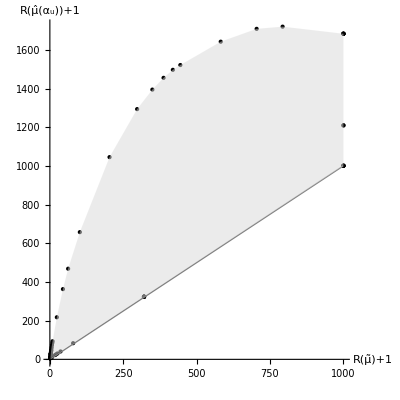

```mathematica
fig1=drawFeasibleSet[f0Data⟦1⟧, PlotStyle->Black]  (* Black points for manuscript *)
```

2 log n =13.8155

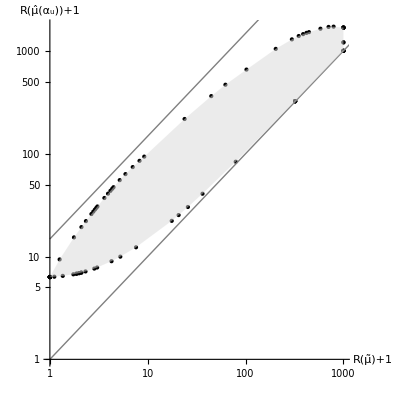

```mathematica
fig2=drawLogFeasibleSet[f0Data⟦1⟧, PlotStyle->Black]
```

These plots are exported below after adding  traces.

### Figure 0A Add paths within the feasible set, illustrating shape

```mathematica
stripCol[x_]:= Sort[#⟦{2,3}⟧&/@x,#1⟦1⟧<#2⟦1⟧&]

With[
{α=1,β=0,ω=0.5,scale=2,n=1000},
With[
{path=StringJoin["~/C/bellman/figures/f0/risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]]},
Print[StringJoin[path,"/m0.5"]];
rr[0.5]  =stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[0.75]=stripCol[Import[StringJoin[path,"/m0.75"], "Table"]];
rr[1.0]=stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
rr[6.0]=stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];

]
]
```

~/C/bellman/figures/f0/risk_alpha100_beta00_omega50_scale2_n1000/m0.5

```mathematica
(* use this to see full import *)
Sort[Import[StringJoin["~/C/bellman/figures/f0/risk_alpha100_beta00_omega50_scale2_n1000/m0.75"], "Table"],
#1⟦1⟧<#2⟦1⟧&]
```

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

This figure omits the trace with μ=0.5 (which is diagonal) and several others to keep graph simple.

```mathematica
?Dashing
```

Dashing[{r_1,r_2,…}] is a two-dimensional graphics directive specifying that lines that follow are to be drawn dashed, with successive segments of lengths r_1, r_2, … (repeated cyclically). The r_i are given as a fraction of the total width of the graph. 
Dashing[r] is equivalent to Dashing[{r,r}].

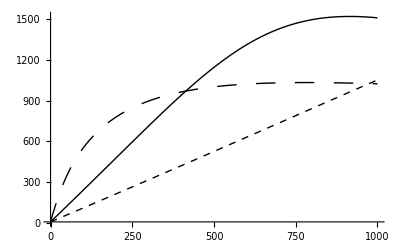

```mathematica
dashing = {Black,Dashing[#]}&/@ {Small, Median,Large};
With[
{μ={1.0,1.5,3.0}},
lp=ListPlot[rr/@μ,
PlotRange->All,
Joined->True,(* PlotLegends->SwatchLegend[μ,LegendLabel->"μ"], *)
PlotStyle->(*{Red,Purple,Blue} *) dashing
]]
```

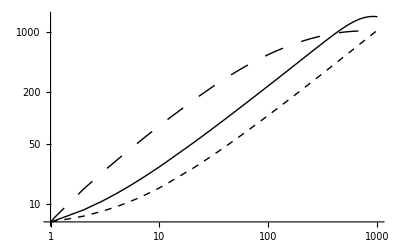

```mathematica
With[
{μ={1.0,1.5,3.0}},
llp=ListLogLogPlot[1+rr/@μ, (* note the extra one being added, as in risk inflation *)
PlotRange->All,
Joined->True,(* PlotLegends->SwatchLegend[μ,LegendLabel->"μ"], *)
PlotStyle->(* {Red,Purple,Blue} *) dashing]
]
```

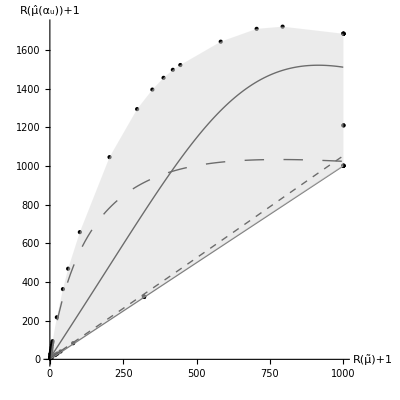

```mathematica
fig11=Show[fig1,lp]
```

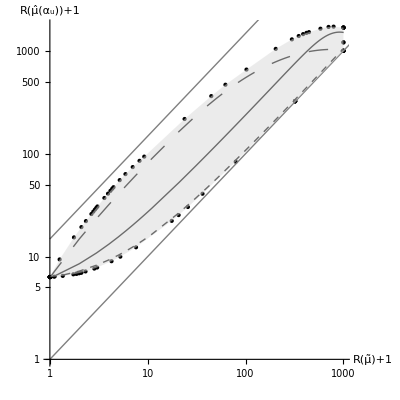

```mathematica
fig22=Show[fig2,llp]
```

```mathematica
Export[StringJoin[figurePath,"riFeasSet_bw.pdf"],fig11]
Export[StringJoin[figurePath,"riFeasSetLog_bw.pdf"],fig22]
```

~/work/papers/alpha-invest/optimal/figures/riFeasSet_bw.pdf

~/work/papers/alpha-invest/optimal/figures/riFeasSetLog_bw.pdf

### Figure 11 Feasible risks: universal bidder with varying W_0 = ω_β, RI oracle

Idea is to show that you want to have a larger payout than might have been expected from usual testing. These first runs vary the initial wealth and payout for a Geometric bidder that spends 1% (or 10%) on the next round.

Note: to get a smooth feasible set, may need to adjust the angles used in the Makefile

```mathematica
id = With[
{α=1,ωα=1,W0α=1,β=0,scale=2,n=1000},
Join[ (* 3 sets of 5 each *)
makeID[{W0α,α,ωα},{   #   ,β,#},scale,n]&/@ {0.05, 0.25,0.50}  (* Subscript[W, 0]=ω *)
]]
```

{{summary_risk_alpha100_100_100_beta05_00_05_scale2_n1000,{{1,1,1},{0.05,0,0.05},2,1000}},{summary_risk_alpha100_100_100_beta25_00_25_scale2_n1000,{{1,1,1},{0.25,0,0.25},2,1000}},{summary_risk_alpha100_100_100_beta50_00_50_scale2_n1000,{{1,1,1},{0.5,0,0.5},2,1000}}}

```mathematica
f11Data=Table[getData[id⟦i⟧,11,"var:"],{i,1,Length[id]}];
```

Examine results for a run to see where convex set is very flat around 90-95 degrees (n=500).

```mathematica
TableForm[f11Data⟦3,3⟧⟦{1,2,3,4,5}⟧]
```

0 | 0.5 | 1000 | 1000 | 1000 | 1208.88
15 | 0.5 | 1000 | 1401.73 | 1000 | 1683.82
30 | 0.5 | 1000 | 1707.94 | 1000 | 1683.82
45 | 0.5 | 1000 | 1897.75 | 1000 | 1683.82
60 | 0.5 | 1000 | 1958.24 | 1000. | 1683.83

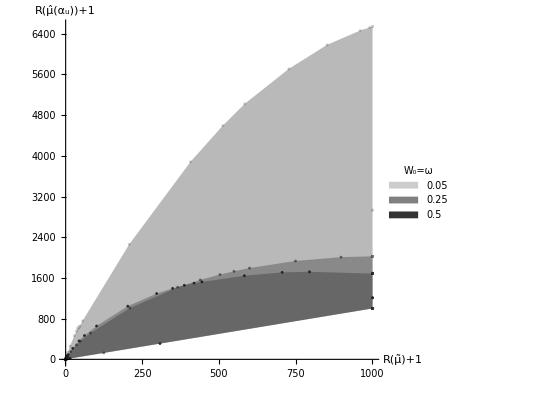

```mathematica
figure11=drawFeasibleSets[
f11Data⟦{1,2,3}⟧, (* omit the ω=0.75 to keep simple *)
{"W_0=ω",getOmegaBeta},
PlotRange->All,
AxesLabel ->{playerName[1,1],playerName[0,ω]}
]
```

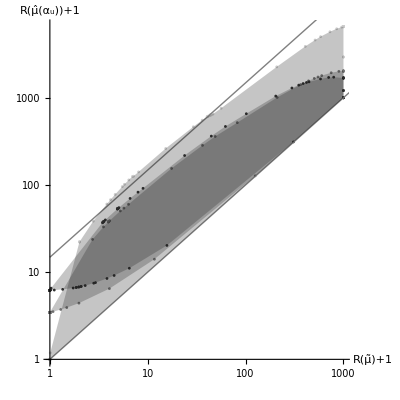

```mathematica
figure11Log=drawLogFeasibleSets[
f11Data⟦{1,2,3}⟧, (* omit the ω=0.75 to keep simple *)
{"W_0=ω",getOmegaBeta},
AxesLabel ->{playerName[1,1],playerName[0,ω]}
]
```

```mathematica
Export[StringJoin[figurePath,"univVsRI_bw.pdf"],figure11]
Export[StringJoin[figurePath,"univVsRILog_bw.pdf"],figure11Log]
```

~/work/papers/alpha-invest/optimal/figures/univVsRI_bw.pdf

~/work/papers/alpha-invest/optimal/figures/univVsRILog_bw.pdf

### Figure 1 Feasible risks: geometric bidder with varying W_0 and ω_β, RI oracle

Idea is to show that you want to have a larger payout than might have been expected from usual testing. These first runs vary the initial wealth and payout for a Geometric bidder that spends 1% (or 10%) on the next round.

Note: to get a smooth feasible set, may need to adjust the angles used in the Makefile

```mathematica
id = With[
{α=1,ωα=1,W0α=1,ωβ=0.25,scale=2,n=500},
Join[ (* 3 sets of 5 each *)
makeID[{W0α,α,ωα},{ ωβ,#,ωβ},scale,n]&/@ {0.001, 0.01,0.05}  (* Subscript[W, 0]=ω *)
(* makeID[{W0α,α,ωα},{0.05,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} ,*) (*Subscript[W, 0]=0.05*)
(* makeID[{W0α,α,ωα},{0.50,β,#},scale,n]&/@ {0.05,0.10,0.25,0.50,0.75}   *)  (*Subscript[W, 0]=0.50*)
]]

f1Data=Table[getData[id⟦i⟧,1,""],{i,1,Length[id]}];
```

{{summary_risk_alpha100_100_100_beta25_001_25_scale2_n500,{{1,1,1},{0.25,0.001,0.25},2,500}},{summary_risk_alpha100_100_100_beta25_01_25_scale2_n500,{{1,1,1},{0.25,0.01,0.25},2,500}},{summary_risk_alpha100_100_100_beta25_05_25_scale2_n500,{{1,1,1},{0.25,0.05,0.25},2,500}}}

Examine results for a run to see where convex set is very flat around 90-95 degrees (n=500).

```mathematica
f1Data⟦2,3⟧⟦{1,2,3,4,5}⟧//TableForm
```

0 | 0.25 | 500 | 500 | 500 | 1208.28
0.05 | 0.25 | 500 | 501.117 | 500 | 1278.28
1 | 0.25 | 500 | 522.231 | 500 | 1278.28
2 | 0.25 | 500 | 544.305 | 500 | 1278.28
4 | 0.25 | 500 | 587.951 | 500 | 1278.28

This version shows the convex hull when W_0=ω.

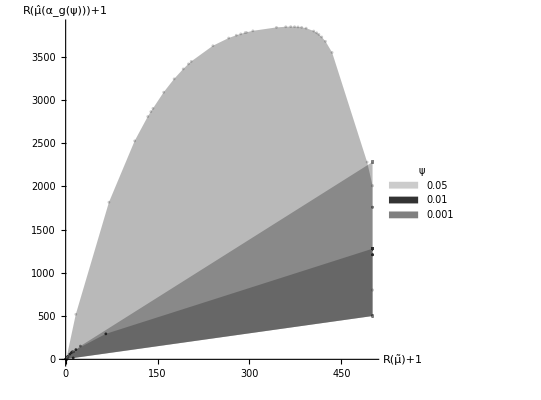

```mathematica
figure1=With[{
β=ToString[getBeta[f1Data⟦1⟧]],  (* Common geometric spending rate *)
n=ToString[getN[f1Data⟦1⟧]]},
drawFeasibleSets[
f1Data⟦{3,2,1}⟧, 
{"ψ",getBeta},
AxesLabel ->{playerName[1,1],playerName[ψ,ω]}]
]
```

```mathematica
Export[StringJoin[figurePath,"geom_bw.pdf"],figure1]
```

~/work/papers/alpha-invest/optimal/figures/geom_bw.pdf

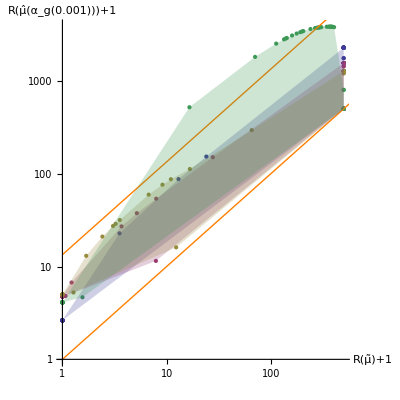

```mathematica
figure1=With[{
β=ToString[getBeta[f1Data⟦1⟧]],  (* Common geometric spending rate *)
n=ToString[getN[f1Data⟦1⟧]]},
drawLogFeasibleSets[
f1Data⟦{1,2,3,4}⟧, (* omit the ω=0.75 to keep simple *)
{"β",getBeta},
AxesLabel ->{playerName[1,1],playerName[β,ω]}]
]
```

Comments on log scale plot:
	Log version for small risks; add one to everything to be logable.  
	Add 1 as in the F&G paper for the forced estimation of an intercept. 
	Feasible set is not convex in this new coordinate system...

2 log n =13.8155

2 log n =13.8155

2 log n =13.8155

«2 more identical outputs»

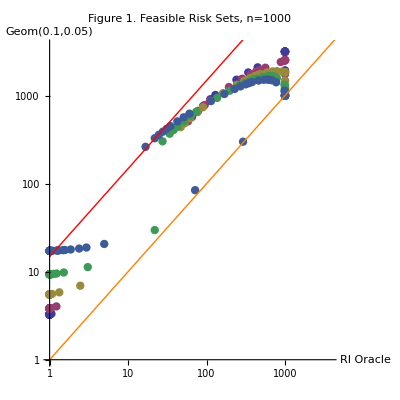

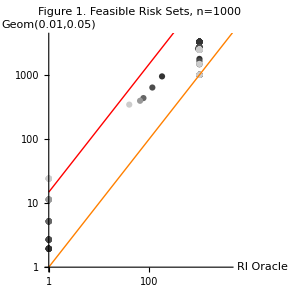

```mathematica
colors=GrayLevel /@ {0.2,0.3,0.4,0.6,0.8};  (* pick colors *)
colors = ColorData[1]/@ {1,2,3,4,5};
f1LogPlots=Table[drawLogFeasibleSet[f1Data⟦i⟧,{False,colors⟦i⟧}],{i,1,5}];
Show[f1LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=1000"]
```

Now fix initial wealth W_0 while allowing ω to vary.  

For (a), the geometric bidder does not get much to start, but can get large payout. 
For (b), it starts with a lot but payout may be small.

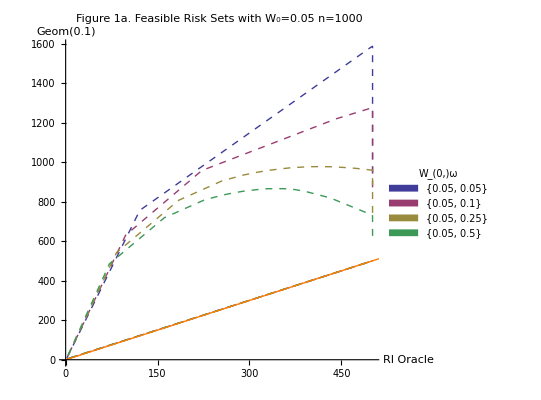

```mathematica
figure1a=With[{
β=ToString[getBeta[f1Data⟦1⟧]],
W0=ToString[getW0Beta[f1Data⟦6⟧]]},
drawFeasibleSets[
f1Data⟦{6,7,8,9}⟧, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1a. Feasible Risk Sets with W_0=",W0," n=1000"],
AxesLabel ->{"RI Oracle",StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashed,#}&/@ColorData[1,"ColorList"]],  Joined->True
]
]
```

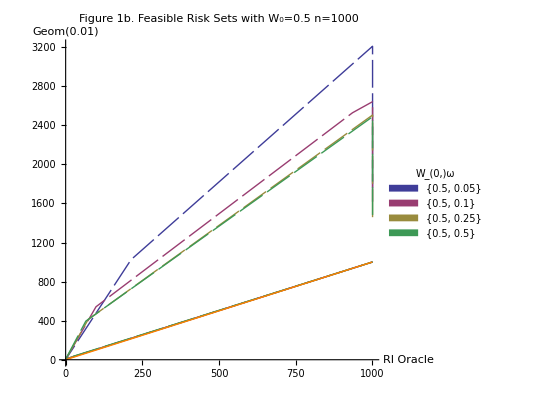

```mathematica
figure1b=With[{
β=ToString[getBeta[f1Data⟦1⟧]],
W0=ToString[getW0Beta[f1Data⟦11⟧]]},
drawFeasibleSets[
f1Data⟦{11,12,13,14}⟧, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1b. Feasible Risk Sets with W_0=",W0," n=1000"],
AxesLabel ->{"RI Oracle",StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashing[{0.05,0.01}],#}&/@ColorData[1,"ColorList"]], 
Joined->True
]
]
```

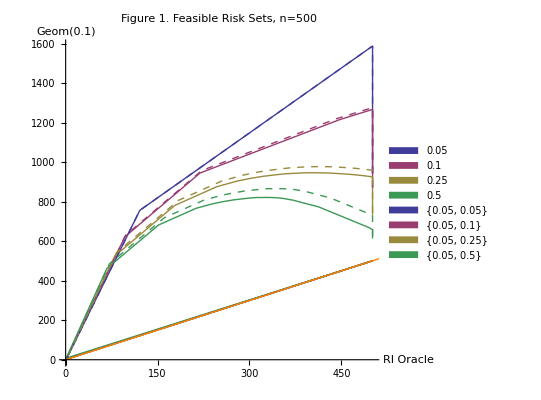

```mathematica
Show[figure1,figure1a]
```

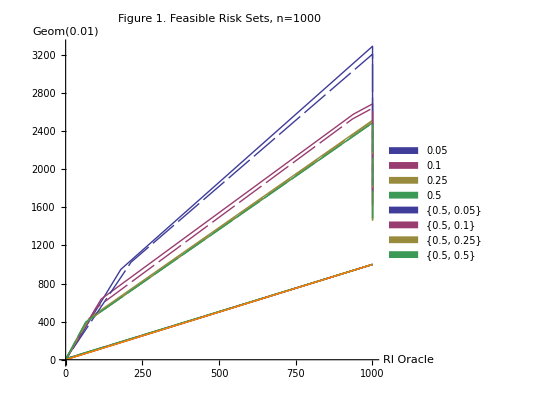

```mathematica
Show[figure1,figure1b]
```

#### Initial wealth effects ...

```mathematica
f1Data[[3,2]]
```

{{1,1,1},{0.5,0.1,0.5},2,500}

```mathematica
f1Data[[7,2]]
```

{{1,1,1},{0.05,0.1,0.5},2,500}

```mathematica
getcol[x_,j_]:= #⟦j⟧&/@x
```

```mathematica
Transpose[Join[Transpose[getcol[f1Data[[3,3]],{3,4,5,6,7,8}]]
,Transpose[getcol[f1Data[[7,3]],{4,8}]]]]//TableForm
```

0 | 0.5 | 500 | -7.18331 | 0 | -7.18331 | 0.5 | -1.90489
15 | 0.5 | 500 | -6.93855 | 0 | -7.18331 | 0.5 | -1.90489
30 | 0.5 | 500 | -6.22093 | 0 | -7.18331 | 0.5 | -1.90489
45 | 0.5 | 500 | -5.07937 | 0 | -7.18331 | 0.5 | -1.90489
60 | 0.5 | 500 | -3.59166 | 0 | -7.18331 | 0.5 | -1.90489
65 | 0.5 | 500 | -3.0358 | 0 | -7.18331 | 0.5 | -1.90489
70 | 0.5 | 500 | -2.45684 | 0 | -7.18331 | 0.5 | -1.90489
75 | 0.5 | 500 | -1.85918 | 0 | -7.18331 | 0.5 | -1.90489
80 | 0.5 | 500 | -1.24737 | 0 | -7.18331 | 0.5 | -1.90489
85 | 0.5 | 500 | -0.626067 | 0 | -7.18331 | 0.5 | -1.90489
90 | 0.5 | 500 | 3.6661×10^-11 | 0 | -7.18331 | 0.5 | -1.90489
91 | 0.5 | 500 | 0.125366 | 0 | -7.18331 | 0.5 | -1.90489
92 | 0.5 | 500 | 0.250694 | 0 | -7.18331 | 0.5 | -1.90489
93 | 0.5 | 500 | 0.375946 | 0 | -7.18331 | 0.5 | -1.90489
93.2 | 0.5 | 500 | 0.400984 | 0 | -7.18331 | 0.5 | -1.90489
93.4 | 0.5 | 500 | 0.426016 | 0 | -7.18331 | 0.5 | -1.90489
93.6 | 0.5 | 500 | 0.451044 | 0 | -7.18331 | 0.5 | -1.90489
93.8 | 0.5 | 500 | 0.476067 | 0 | -7.18331 | 0.5 | -1.90489
94 | 0.5 | 500 | 0.501083 | 0 | -7.18331 | 0.5 | -1.90489
94.2 | 0.5 | 500 | 0.526093 | 0 | -7.18331 | 0.5 | -1.90489
94.4 | 0.5 | 500 | 0.551097 | 0 | -7.18331 | 0.5 | -1.90489
94.6 | 0.5 | 500 | 0.576094 | 0 | -7.18331 | 0.5 | -1.90489
94.8 | 0.5 | 500 | 0.601085 | 0 | -7.18331 | 0.5 | -1.90489
95 | 0.5 | 500 | 0.626067 | 0 | -7.18331 | 0.5 | -1.90489
95.2 | 0.5 | 500 | 0.752366 | -10.7728 | -126.675 | 0.5 | -130.157
95.4 | 0.5 | 500 | 1.22536 | -12.0921 | -140.941 | 0.5 | -144.805
95.6 | 0.5 | 500 | 1.71763 | -12.6877 | -147.001 | 0.5 | -150.995
95.8 | 0.5 | 500 | 2.31029 | -14.0084 | -160.772 | 0.5 | -165.593
96 | 0.5 | 500 | 3.00357 | -15.7059 | -178.166 | 0.5 | -184.095
96.2 | 0.5 | 500 | 3.64537 | -16.5818 | -186.392 | 0.5 | -192.752
96.4 | 0.5 | 500 | 4.31301 | -17.4808 | -194.537 | 0.5 | -201.33
96.6 | 0.5 | 500 | 5.00828 | -18.3762 | -202.395 | 0.5 | -209.622
96.8 | 0.5 | 500 | 5.73082 | -19.2632 | -209.947 | 0.5 | -217.609
97 | 0.5 | 500 | 6.47853 | -20.0944 | -216.815 | 0.5 | -224.919
98 | 0.5 | 500 | 10.5188 | -24.5458 | -250.233 | 0.5 | -260.309
99 | 0.5 | 500 | 15.3458 | -30.1737 | -288.606 | 0.5 | -300.958
100 | 0.5 | 500 | 20.6994 | -35.7738 | -322.086 | 0.5 | -336.439
105 | 0.5 | 500 | 55.3742 | -66.3424 | -461.543 | 0.5 | -484.568
110 | 0.5 | 500 | 100.184 | -96.2019 | -557.23 | 0.5 | -586.156
115 | 0.5 | 500 | 153.278 | -128.996 | -639.321 | 0.5 | -673.327
120 | 0.5 | 500 | 210.176 | -150.771 | -681.495 | 0.5 | -718.069
125 | 0.5 | 500 | 270.226 | -174.91 | -720.922 | 0.5 | -759.882
135 | 0.5 | 500 | 391.67 | -211.954 | -765.856 | 0.5 | -807.519
150 | 0.5 | 500 | 564.512 | -256.864 | -800.145 | 0.5 | -843.64
165 | 0.5 | 500 | 712.561 | -300.062 | -818.099 | 0.5 | -862.534
180 | 0.5 | 500 | 820.883 | -327.311 | -820.883 | 0.5 | -865.44
195 | 0.5 | 500 | 880.188 | -346.686 | -818.344 | 0.5 | -862.808
210 | 0.5 | 500 | 884.085 | -369.455 | -807.55 | 0.5 | -851.666
225 | 0.5 | 500 | 837.915 | -412.344 | -772.647 | 0.5 | -818.426
240 | 0.5 | 500 | 762.088 | -493.942 | -668.643 | 0.5 | -736.592
255 | 0.5 | 500 | 653.037 | -499.999 | -657.124 | 0.5 | -728.258
270 | 0.5 | 500 | 500 | -500 | -500.036 | 0.5 | -500.035
285 | 0.5 | 500 | 353.552 | -500 | -500 | 0.5 | -500
300 | 0.5 | 500 | 183.013 | -500 | -500 | 0.5 | -500
315 | 0.5 | 500 | -1.26286×10^-8 | -500 | -500 | 0.5 | -500
330 | 0.5 | 500 | -6.22087 | -0.00129951 | -7.18399 | 0.5 | -1.90557
345 | 0.5 | 500 | -6.93855 | -1.25446×10^-6 | -7.18332 | 0.5 | -1.90489
359 | 0.5 | 500 | -7.18222 | 0 | -7.18331 | 0.5 | -1.90489

#### Saved

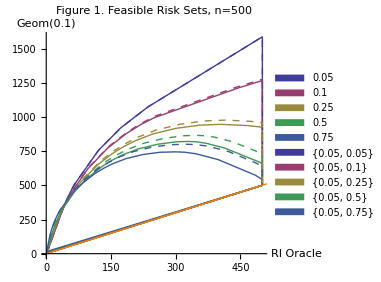
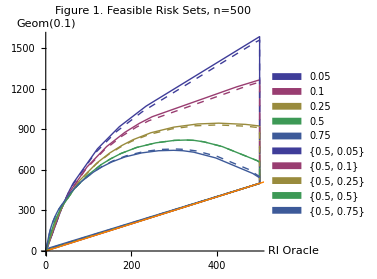

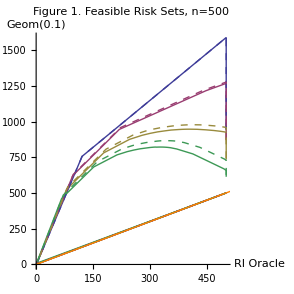

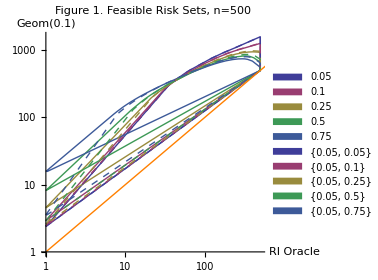
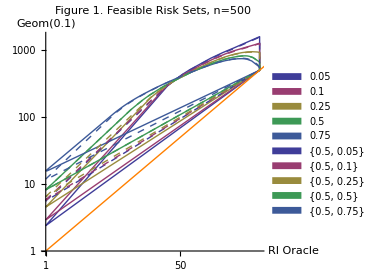

At a lower geometric spending rate β=0.01, the plot is more congested (all lose for high signal), but you really see problems with the high value for ω=0.75 in the low signal case.  You don’t gain by having ω=0.75 with high signal (you’re spending too slowly) but get bashed for little signal.  Setting the initial value to 0.05 in that case helps, but only for a little while.

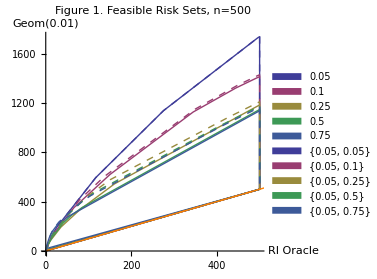
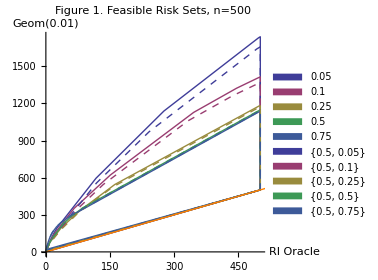

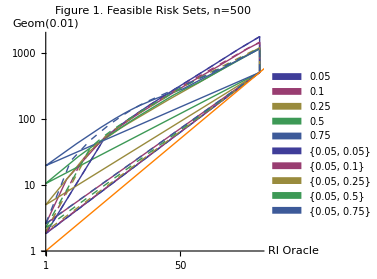
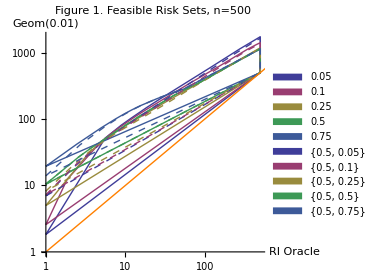

### Figure 2 Feasible risks: geometric bidder with varying W_0 and ω_β, testimator oracle

Idea now is to reproduce the prior figures, but with a different oracle that is a fixed testimator (no wealth constraint, just a given testimator).

```mathematica
id = With[
{W0α=1,α=0.1,ωα=1,β=0.1,scale=2,n=1000},
Join[ (* 3 sets of 5 each *)
makeID[{W0α,α,ωα},{   #   ,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (* Subscript[W, 0]=ω *)
makeID[{W0α,α,ωα},{0.05,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (*Subscript[W, 0]=0.05*)
makeID[{W0α,α,ωα},{0.50,β,#},scale,n]&/@ {0.05,0.10,0.25,0.50,0.75}     (*Subscript[W, 0]=0.50*)
]]

f2Data=Table[getData[id⟦i⟧,1,"variance:"],{i,1,Length[id]}];
```

{{summary_risk_alpha100_10_100_beta05_10_05_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.05},2,1000}},{summary_risk_alpha100_10_100_beta10_10_10_scale2_n1000,{{1,0.1,1},{0.1,0.1,0.1},2,1000}},{summary_risk_alpha100_10_100_beta25_10_25_scale2_n1000,{{1,0.1,1},{0.25,0.1,0.25},2,1000}},{summary_risk_alpha100_10_100_beta50_10_50_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.5},2,1000}},{summary_risk_alpha100_10_100_beta75_10_75_scale2_n1000,{{1,0.1,1},{0.75,0.1,0.75},2,1000}},{summary_risk_alpha100_10_100_beta05_10_05_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.05},2,1000}},{summary_risk_alpha100_10_100_beta05_10_10_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.1},2,1000}},{summary_risk_alpha100_10_100_beta05_10_25_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.25},2,1000}},{summary_risk_alpha100_10_100_beta05_10_50_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.5},2,1000}},{summary_risk_alpha100_10_100_beta05_10_75_scale2_n1000,{{1,0.1,1},{0.05,0.1,0.75},2,1000}},{summary_risk_alpha100_10_100_beta50_10_05_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.05},2,1000}},{summary_risk_alpha100_10_100_beta50_10_10_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.1},2,1000}},{summary_risk_alpha100_10_100_beta50_10_25_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.25},2,1000}},{summary_risk_alpha100_10_100_beta50_10_50_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.5},2,1000}},{summary_risk_alpha100_10_100_beta50_10_75_scale2_n1000,{{1,0.1,1},{0.5,0.1,0.75},2,1000}}}

Look for the angle where risk increases suddenly.

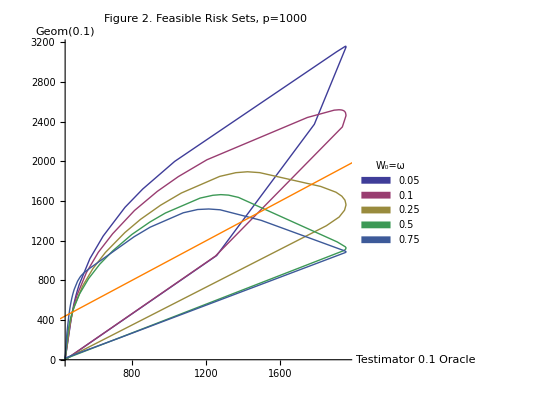

```mathematica
With[ {data=f2Data⟦{1,2,3,4,5}⟧},
figure2=With[
{α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]],(* Common geometric spending rate *)
n=ToString[getN[data⟦1⟧]]}, 
drawFeasibleSets[
data, (* omit the ω=0.75 to keep simple *)
{"W_0=ω",getOmegaBeta},
PlotLabel->StringJoin["Figure 2. Feasible Risk Sets, p=",n],
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]]
```

Log scale is less interesting for these having seen them for the prior example.

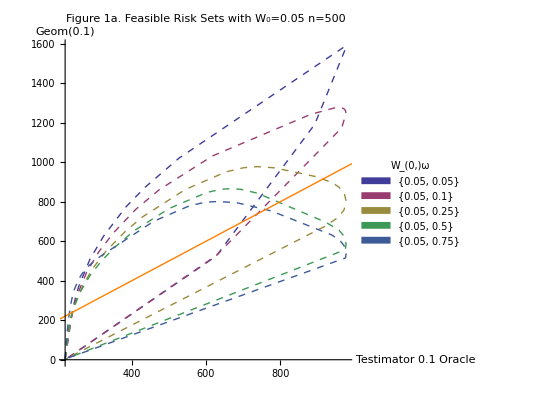

```mathematica
With[ {data=f2Data⟦{6,7,8,9,10}⟧},
figure2a=With[{
α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]],
W0=ToString[getW0Beta[data⟦1⟧]]},
drawFeasibleSets[
data, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1a. Feasible Risk Sets with W_0=",W0," n=500"],
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashed,#}&/@ColorData[1,"ColorList"]],  Joined->True
]
]]
```

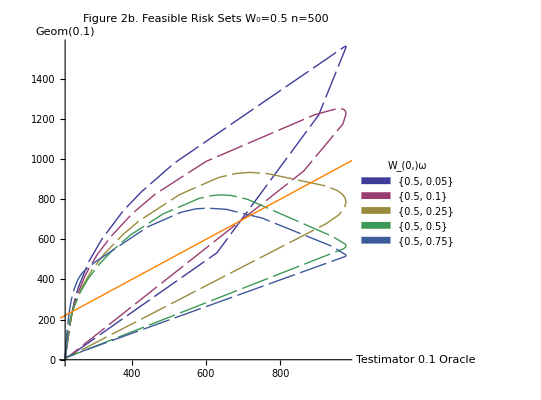

```mathematica
With[ {data=f2Data⟦{11,12,13,14,15}⟧},
figure2b=With[{
α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]],
W0=ToString[getW0Beta[data⟦1⟧]]},
drawFeasibleSets[
data, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 2b. Feasible Risk Sets  W_0=",W0," n=500"],
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashing[{0.05,0.01}],#}&/@ColorData[1,"ColorList"]], 
Joined->True
]]]
```

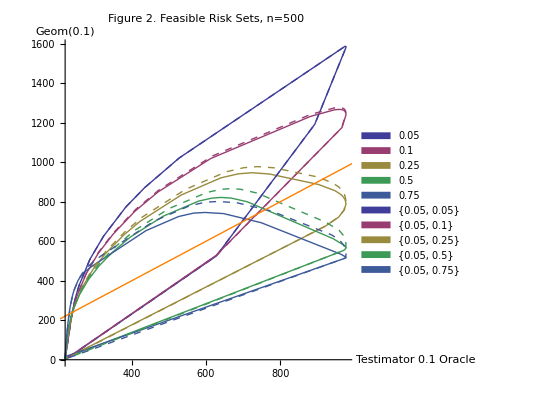

```mathematica
Show[figure2, figure2a]
```

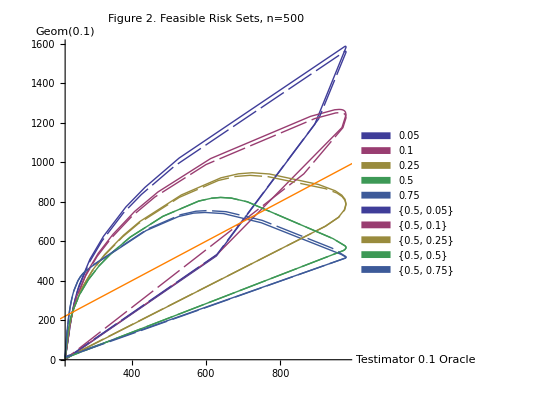

```mathematica
Show[figure2, figure2b]
```

### Figure 3 Paths within the feasible set, illustrating shape

This figure shows paths within the feasible set produced by non-zero means that occur with varying probabilities and varying sizes. The concave shape of the path within the feasible set shows that we are only gettin the convex boundary.  The figures require the data from figure 2 to show the boundary, then put these paths within that set.

```mathematica
stripCol[x_]:= #⟦{2,3}⟧&/@x

With[
{α=0.10,β=0.10,ω=0.5,scale=2,n=500},
With[
{path=StringJoin["~/C/bellman/figures/f3/risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]]},
Print[StringJoin[path,"/m0.5"]];
rr[0.5]=-stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[1.0]=-stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=-stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=-stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=-stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=-stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=-stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=-stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
]
]
```

~/C/bellman/figures/f3/risk_alpha10_beta10_omega50_scale2_n500/m0.5

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

```mathematica
With[
{μ={0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0}},
lp=ListPlot[rr/@μ,
PlotRange->All,
Joined->True,PlotLegends->SwatchLegend[μ,LegendLabel->"μ"],
PlotStyle->GrayLevel/@Range[0.9,0.1,-0.1]]
]
```

```mathematica
fp=drawFeasibleSet[f2Data⟦3⟧,{True,Blue}]
```

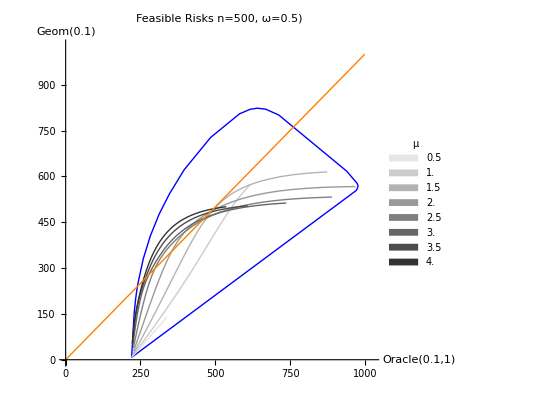

```mathematica
Show[fp,lp]
```

### Figure 4 Comparison of geometric bidders with different ω

```mathematica
id =With[
{α=0.1,ω1=0.05,β=0.1,ω2=0.50,scale=2,n=1000},
{makeID[{ω1,α        ,ω1},{ω2,β        ,ω2},scale,n],
makeID[{ω1,α/10,ω1},{ω2,β        ,ω2},scale,n],
makeID[{ω1,α         ,ω1},{ω2,β/10,ω2},scale,n],
makeID[{ω1,α/10 ,ω1},{ω2,β/10,ω2},scale,n]}
]

f4Data=Table[getData[id⟦i⟧,4,"variance:"],{i,1,Length[id]}];
```

{{summary_risk_alpha05_10_05_beta50_10_50_scale2_n1000,{{0.05,0.1,0.05},{0.5,0.1,0.5},2,1000}},{summary_risk_alpha05_01_05_beta50_10_50_scale2_n1000,{{0.05,0.01,0.05},{0.5,0.1,0.5},2,1000}},{summary_risk_alpha05_10_05_beta50_01_50_scale2_n1000,{{0.05,0.1,0.05},{0.5,0.01,0.5},2,1000}},{summary_risk_alpha05_01_05_beta50_01_50_scale2_n1000,{{0.05,0.01,0.05},{0.5,0.01,0.5},2,1000}}}

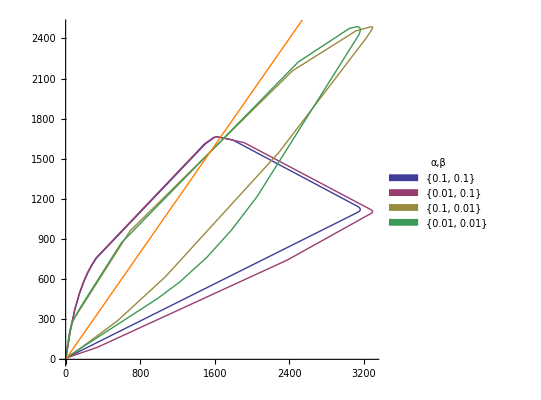

```mathematica
drawFeasibleSets[f4Data,{"α,β",getAlphaBeta},Joined->True]
```

### Figure 5 Comparison of universal versus geometric bidders with different probabilities

#### Figures from Stat Comp and Simulation paper.

```mathematica
id =With[
{scale=2,n=1000},
makeID[{0.25,#,0.25},{0.25,0,0.25},scale,n]&/@{0.001,0.002,0.005}
]

f5Data=Table[getData[id⟦i⟧,5,"variance:"],{i,1,Length[id]}];
```

{{summary_risk_alpha25_001_25_beta25_00_25_scale2_n1000,{{0.25,0.001,0.25},{0.25,0,0.25},2,1000}},{summary_risk_alpha25_002_25_beta25_00_25_scale2_n1000,{{0.25,0.002,0.25},{0.25,0,0.25},2,1000}},{summary_risk_alpha25_005_25_beta25_00_25_scale2_n1000,{{0.25,0.005,0.25},{0.25,0,0.25},2,1000}}}

```mathematica
f5Data⟦1,3⟧⟦{1,2,3,4,5}⟧//TableForm
```

0 | 250.25 | 1000 | 4509.82 | 4509.82 | 1253.04
15 | 250.25 | 1000 | 4682.72 | 4507.29 | 1271.41
30 | 250.25 | 1000 | 4542.39 | 4496.42 | 1296.68
45 | 250.25 | 1000 | 4102.59 | 4461.74 | 1340.14
60 | 250.25 | 1000 | 3409.9 | 4310.59 | 1448.69

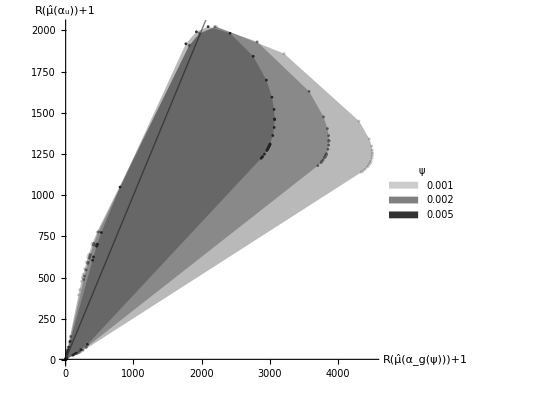

```mathematica
figure5=drawFeasibleSets[
f5Data,
{"ψ",getAlpha},
Diagonal->True,
PlotRange->All,
AxesLabel ->{playerName[ψ,0.25],playerName[0,0.25]}
]
```

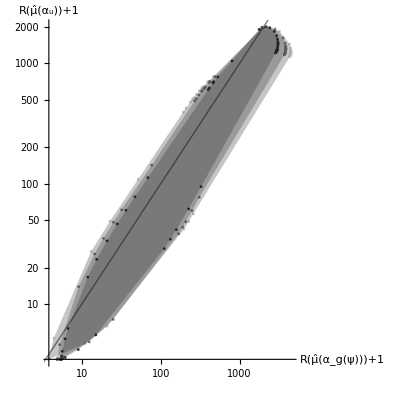

```mathematica
figure5Log=drawLogFeasibleSets[
f5Data,
{"ψ",getAlpha},
RIDiagonal->False,
PlotRange->All,
AxesLabel ->{playerName[ψ,0.25],playerName[0,0.25]}
]
```

```mathematica
Export[StringJoin[figurePath,"univGeo_bw.pdf"],figure5]
Export[StringJoin[figurePath,"univGeoLog_bw.pdf"],figure5Log]
```

~/work/papers/alpha-invest/optimal/figures/univGeo_bw.pdf

~/work/papers/alpha-invest/optimal/figures/univGeoLog_bw.pdf

Update these to show the plots with the universal bidder (0.25,0.25) on the x axis (basically swapping X-Y), and then add the comparison bounds

#### Comparison of Geometric to Universal (0.25,0.25) expert

These are the angles for the roughly 2 to 1 comparison ratio so can compare results of running the Bellman feasible set to the optimizer alone.

```mathematica
{ArcTan[1,-1], ArcTan[1.,-2],ArcTan[1.,-2.5],ArcTan[1.,-3]}
```

{-π/4,-1.10715,-1.19029,-1.24905}

```mathematica
360+360/(2π){ArcTan[1,-1], ArcTan[1.,-2],ArcTan[1.,-2.5],ArcTan[1.,-3]}
```

{315,296.565,291.801,288.435}

Get the data.  Make sure that the system has a destination directory or will get ‘file not found’ error.

```mathematica
id =With[
{scale=2,n=200},
makeID[{0.25,0,0.25},{0.25,#,0.25},scale,n]&/@{0.0001,0.001,0.01,0.1, 0.25,0.35}
]

f5Data=Table[getData[id⟦i⟧,51,"variance:"],{i,1,Length[id]}];
```

{{summary_risk_alpha25_00_25_beta25_0001_25_scale2_n200,{{0.25,0,0.25},{0.25,0.0001,0.25},2,200}},{summary_risk_alpha25_00_25_beta25_001_25_scale2_n200,{{0.25,0,0.25},{0.25,0.001,0.25},2,200}},{summary_risk_alpha25_00_25_beta25_01_25_scale2_n200,{{0.25,0,0.25},{0.25,0.01,0.25},2,200}},{summary_risk_alpha25_00_25_beta25_10_25_scale2_n200,{{0.25,0,0.25},{0.25,0.1,0.25},2,200}},{summary_risk_alpha25_00_25_beta25_25_25_scale2_n200,{{0.25,0,0.25},{0.25,0.25,0.25},2,200}},{summary_risk_alpha25_00_25_beta25_35_25_scale2_n200,{{0.25,0,0.25},{0.25,0.35,0.25},2,200}}}

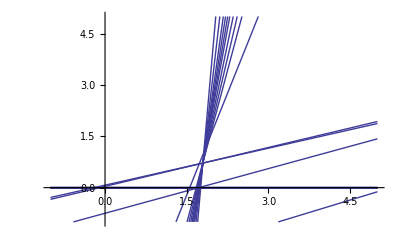

```mathematica
tp=plotTangentBundle[pickColumns[f5Data⟦2,3⟧],{-1,5}]
```

```mathematica
With[ 
{table=f5Data⟦2⟧},
Print[ ψ,"=",getBeta[table]];
table⟦3⟧⟦Range[10,50]⟧//TableForm[#,TableHeadings->{None,{"Degree","Omegas","n","Util","x","y"}}]&
]
```

ψ=0.001

Degree | Omegas | n | Util | x | y
135 | 250.25 | 200 | 490.077 | 245.375 | 938.45
140 | 250.25 | 200 | 415.367 | 243.582 | 936.487
145 | 250.25 | 200 | 337.754 | 241.577 | 933.864
150 | 250.25 | 200 | 257.898 | 239.29 | 930.259
155 | 250.25 | 200 | 176.514 | 236.606 | 925.071
160 | 250.25 | 200 | 94.4039 | 233.345 | 917.129
165 | 250.25 | 200 | 12.5307 | 229.189 | 903.762
170 | 250.25 | 200 | -1.63627 | 1.91258 | 1.42391
171 | 250.25 | 200 | -1.66017 | 1.80367 | 0.775334
172 | 250.25 | 200 | -1.67785 | 1.796 | 0.723346
173 | 250.25 | 200 | -1.69443 | 1.79555 | 0.719937
173.5 | 250.25 | 200 | -1.70251 | 1.79551 | 0.719539
174 | 250.25 | 200 | -1.71046 | 1.79548 | 0.719294
174.5 | 250.25 | 200 | -1.71827 | 1.79547 | 0.71921
175 | 250.25 | 200 | -1.72596 | 1.79547 | 0.719148
176 | 250.25 | 200 | -1.74093 | 1.79546 | 0.719111
177 | 250.25 | 200 | -1.75537 | 1.79546 | 0.7191
178 | 250.25 | 200 | -1.76927 | 1.79546 | 0.7191
179 | 250.25 | 200 | -1.78264 | 1.79546 | 0.7191
180 | 250.25 | 200 | -1.79546 | 1.79546 | 0.7191
195 | 250.25 | 200 | -1.9204 | 1.79546 | 0.7191
210 | 250.25 | 200 | -1.91447 | 1.79546 | 0.7191
225 | 250.25 | 200 | -1.77807 | 1.79546 | 0.7191
240 | 250.25 | 200 | -1.52049 | 1.79546 | 0.7191
255 | 250.25 | 200 | -1.1593 | 1.79546 | 0.7191
270 | 250.25 | 200 | -0.7191 | 1.79546 | 0.7191
275 | 250.25 | 200 | -0.559878 | 1.79546 | 0.7191
280 | 250.25 | 200 | -0.396396 | 1.79546 | 0.7191
285 | 250.25 | 200 | -0.229897 | 1.79546 | 0.7191
290 | 250.25 | 200 | -0.0613542 | 1.87369 | 0.747261
291.801 | 250.25 | 200 | 0.240054 | 14.0263 | 5.35184
295 | 250.25 | 200 | 1.72319 | 36.697 | 15.2107
296.565 | 250.25 | 200 | 3.00548 | 50.3058 | 21.7926
300 | 250.25 | 200 | 7.81561 | 90.7905 | 43.3932
305 | 250.25 | 200 | 17.9646 | 116.582 | 59.7011
306 | 250.25 | 200 | 20.2831 | 121.482 | 63.1902
307 | 250.25 | 200 | 22.6637 | 124.391 | 65.357
308 | 250.25 | 200 | 25.0958 | 126.507 | 66.9912
309 | 250.25 | 200 | 27.5766 | 135.591 | 74.3151
310 | 250.25 | 200 | 30.2566 | 137.88 | 76.1981
311 | 250.25 | 200 | 32.9702 | 139.52 | 77.5969

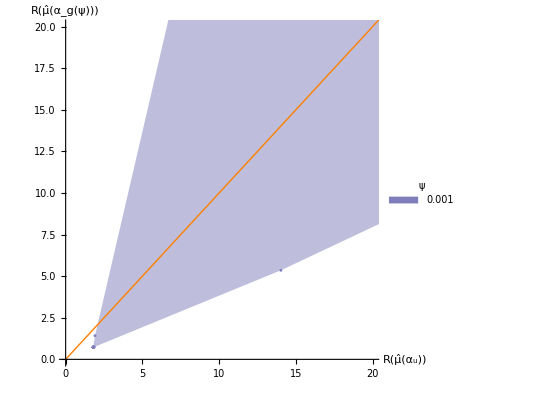

```mathematica
With[{inflated=False},
figure5=drawFeasibleSets[
f5Data⟦{2}⟧,
{"ψ",getBeta},
Diagonal->True,Bounds->inflated,
PlotRange->{{0,80},{0,80}},
AxesLabel ->{
playerName[0,0.25],
If[inflated,inflateRisk[playerName[ψ,0.25]], playerName[ψ,0.25]]}
]]
```

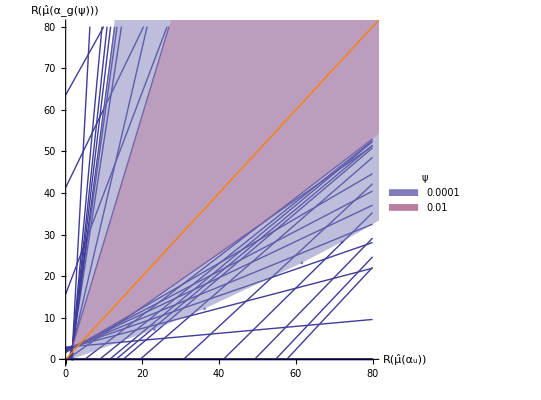

```mathematica
Show[figure5,tp]
```

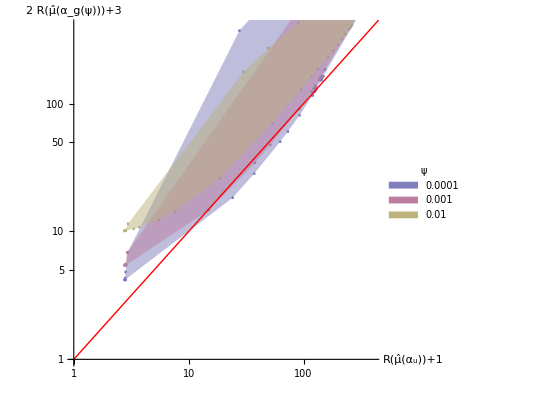

```mathematica
figure5Log=drawLogFeasibleSets[
f5Data⟦{1,2,3}⟧,
{"ψ",getBeta},
RIDiagonal->False,Bounds->True,
PlotRange->{{1,400},{1,400}},
AxesLabel ->{1+playerName[0,0.25],1+inflateRisk[playerName[ψ,0.25]]}
]
```

```mathematica
Export[StringJoin[figurePath,"univGeo_bw.pdf"],figure5]
Export[StringJoin[figurePath,"univGeoLog_bw.pdf"],figure5Log]
```

~/work/papers/alpha-invest/optimal/figures/univGeo_bw.pdf

~/work/papers/alpha-invest/optimal/figures/univGeoLog_bw.pdf

Update these to show the plots with the universal bidder (0.25,0.25) on the x axis (basically swapping X-Y), and then add the comparison bounds

### Figure 6 Compare two testimators, unconstrained

Can do this one analytically since there is no state; keep constant wealth set by W_0.  Just maximize the comparitive risk.  

The figure here is more a way of aligning the C++ output to a simpler presentation arrangement, such as getting rid of the negative risk formulation and using a cosine/sine x-y pairing.  See the analysis in Risk.nb

```mathematica
figure = 6;
id = With[
{W0α=0.05,α=1,ωα=1,β=1,ωβ=1,scale=2,n=500},
makeID[{W0α,α,ωα},{# ,β,ωβ},scale,n]& /@ {0.10,0.15,0.20}
]

f6Data=Table[getData[id⟦i⟧,figure,""],{i,1,Length[id]}];
```

Examine results for a run to see where convex set is very flat around 90-95 degrees (n=500).

```mathematica
Take[f6Data⟦1,3⟧,30]//TableForm
```

This version shows the convex hull when W_0=ω.

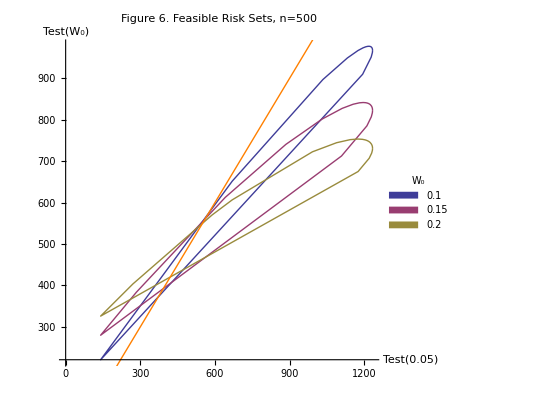

```mathematica
With[{data=f6Data},
figure6=With[{
α=ToString[getW0Alpha[data⟦1⟧]],
β=ToString[getW0Beta[data⟦1⟧]]
}, 
drawFeasibleSets[
data, (* omit the ω=0.75 to keep simple *)
{"W_0",getW0Beta},
PlotLabel->"Figure 6. Feasible Risk Sets, n=500",
AxesLabel ->{StringJoin["Test(",α,")"],StringJoin["Test(","W_0",")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]]
```

### Figure X Compare universal bidders with different payouts, base ω=0.5

```mathematica
id =With[
{scale=2,n=200},
{
makeID[{.5,0,.5},{.45,0,.45},scale,n], 
makeID[{.5,0,.5},{.35,0,.35},scale,n], 
makeID[{.5,0,.5},{.25,0,.25},scale,n], 
makeID[{.5,0,.5},{.10,0,.10},scale,n], 
makeID[{.5,0,.5},{.05,0,.05},scale,n]
}
]

fXData=Table[getData[id⟦i⟧,"X","var:"],{i,1,Length[id]}]; 
{Length[fXData], Dimensions[fXData⟦1,3⟧]}
```

{{summary_risk_alpha50_00_50_beta45_00_45_scale2_n200,{{0.5,0,0.5},{0.45,0,0.45},2,200}},{summary_risk_alpha50_00_50_beta35_00_35_scale2_n200,{{0.5,0,0.5},{0.35,0,0.35},2,200}},{summary_risk_alpha50_00_50_beta25_00_25_scale2_n200,{{0.5,0,0.5},{0.25,0,0.25},2,200}},{summary_risk_alpha50_00_50_beta10_00_10_scale2_n200,{{0.5,0,0.5},{0.1,0,0.1},2,200}},{summary_risk_alpha50_00_50_beta05_00_05_scale2_n200,{{0.5,0,0.5},{0.05,0,0.05},2,200}}}

{5,{62,6}}

Use this one to see it all

```mathematica
fXData⟦5,3⟧//TableForm
```

Or just a part

```mathematica
fXData⟦1,3⟧⟦{1,2,3,4,5}⟧//TableForm
```

0 | 500.45 | 200 | 341.991 | 341.991 | 330.323
15 | 500.45 | 200 | 417.225 | 339.797 | 343.894
30 | 500.45 | 200 | 466.979 | 338.389 | 347.85
45 | 500.45 | 200 | 485.364 | 337.912 | 348.496
60 | 500.45 | 200 | 470.829 | 337.512 | 348.804

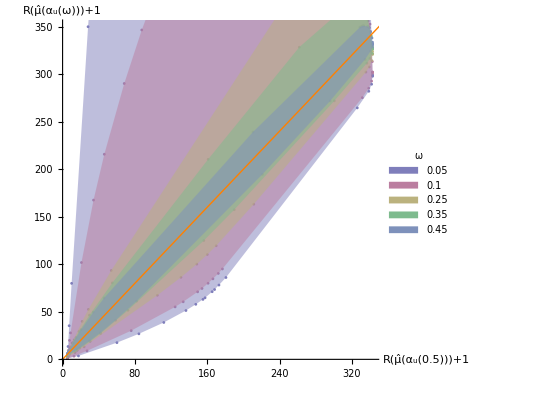

```mathematica
figureY=drawFeasibleSets[
fXData[[{5,4,3,2,1}]],
{"ω",getOmega},
Diagonal->True,
PlotRange->{All,{0,350}},
AxesLabel ->{universalName[0.5],universalName[ω]}
]
```

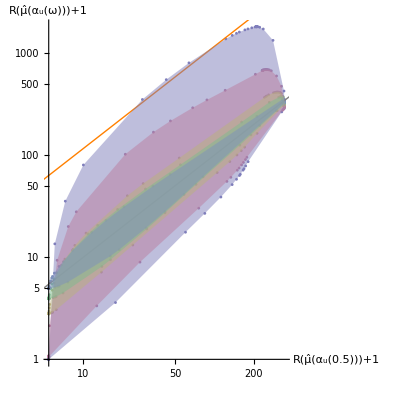

```mathematica
figureYLog=drawLogFeasibleSets[
fXData[[{5,4,3,2,1}]],
{"ω",getOmega},
RIDiagonal->True,
PlotRange->All,
AxesLabel ->{universalName[0.5],universalName[ω]}
]
```

```mathematica
Export["~/Desktop/figure.pdf",figureY]
Export["~/Desktop/figureLog.pdf",figureYLog]
```

### Figure Y Compare universal bidders with different payouts, base ω=0.25

```mathematica
alpha = {0.02, 0.05, 0.10,0.15,0.20,         0.30,0.35,0.40,0.45,0.50,0.60, 0.70,0.90}
id =With[
{scale=2,n=200},
Table[makeID[{.25,0,.25},{alpha⟦j⟧,0,alpha⟦j⟧},scale,n], {j,1,Length[alpha]}]
]

fYData=Table[getData[id⟦i⟧,"Y","var:"],{i,1,Length[id]}]; 
{Length[fYData], Dimensions[fYData⟦1,3⟧]}
```

{0.02,0.05,0.1,0.15,0.2,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.9}

{{summary_risk_alpha25_00_25_beta02_00_02_scale2_n200,{{0.25,0,0.25},{0.02,0,0.02},2,200}},{summary_risk_alpha25_00_25_beta05_00_05_scale2_n200,{{0.25,0,0.25},{0.05,0,0.05},2,200}},{summary_risk_alpha25_00_25_beta10_00_10_scale2_n200,{{0.25,0,0.25},{0.1,0,0.1},2,200}},{summary_risk_alpha25_00_25_beta15_00_15_scale2_n200,{{0.25,0,0.25},{0.15,0,0.15},2,200}},{summary_risk_alpha25_00_25_beta20_00_20_scale2_n200,{{0.25,0,0.25},{0.2,0,0.2},2,200}},{summary_risk_alpha25_00_25_beta30_00_30_scale2_n200,{{0.25,0,0.25},{0.3,0,0.3},2,200}},{summary_risk_alpha25_00_25_beta35_00_35_scale2_n200,{{0.25,0,0.25},{0.35,0,0.35},2,200}},{summary_risk_alpha25_00_25_beta40_00_40_scale2_n200,{{0.25,0,0.25},{0.4,0,0.4},2,200}},{summary_risk_alpha25_00_25_beta45_00_45_scale2_n200,{{0.25,0,0.25},{0.45,0,0.45},2,200}},{summary_risk_alpha25_00_25_beta50_00_50_scale2_n200,{{0.25,0,0.25},{0.5,0,0.5},2,200}},{summary_risk_alpha25_00_25_beta60_00_60_scale2_n200,{{0.25,0,0.25},{0.6,0,0.6},2,200}},{summary_risk_alpha25_00_25_beta70_00_70_scale2_n200,{{0.25,0,0.25},{0.7,0,0.7},2,200}},{summary_risk_alpha25_00_25_beta90_00_90_scale2_n200,{{0.25,0,0.25},{0.9,0,0.9},2,200}}}

{13,{73,6}}

```mathematica
fYData⟦1,3⟧//TableForm
```

```mathematica
fYData⟦1,3⟧⟦{1,2,3,4,5}⟧//TableForm
```

0 | 250.05 | 200 | 412.508 | 412.508 | 447.647
2.5 | 250.05 | 200 | 432.201 | 411.082 | 493.115
5 | 250.05 | 200 | 458.495 | 384.744 | 862.997
10 | 250.05 | 200 | 574.048 | 291.419 | 1653.09
15 | 250.05 | 200 | 715.673 | 269.161 | 1760.63

#### Simple analysis of the minimum risks for these experts ...

```mathematica
(t=Table[Min/@ Transpose[fYData⟦j,3⟧]⟦{5,6}⟧,{j,1,13}])//TableForm
```

1.79546 | 0
1.79546 | 0.000025379
1.79546 | 0.0556335
1.79546 | 0.529858
1.79546 | 1.17222
1.79546 | 2.37627
1.79546 | 2.91921
1.79546 | 3.44954
1.79546 | 3.94797
1.79546 | 4.43982
1.79546 | 5.45758
1.79546 | 6.66405
1.79546 | 13.1459

{0.02,0.05,0.1,0.15,0.2,0.25,0.35,0.4,0.45,0.5,0.6,0.7,0.9}

{0,0.000025379,0.0556335,0.529858,1.17222,1.795,2.91921,3.44954,3.94797,4.43982,5.45758,6.66405,13.1459}

{{0.02,0},{0.05,0.000025379},{0.1,0.0556335},{0.15,0.529858},{0.2,1.17222},{0.25,1.795},{0.35,2.91921},{0.4,3.44954},{0.45,3.94797},{0.5,4.43982},{0.6,5.45758},{0.7,6.66405},{0.9,13.1459}}

-1.0093+10.9502 x

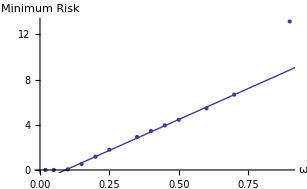

```mathematica
allAlpha =Join[ alpha⟦{1,2,3,4,5}⟧,{0.25},alpha⟦{7,8,9,10,11,12,13}⟧ ](* splice in 0.25 *)
y = Transpose[t]⟦2⟧;
y                 =      Join[ y⟦{1,2,3,4,5}⟧,{1.795},y⟦{7,8,9,10,11,12,13}⟧ ]
xy=Transpose[{allAlpha,y}]
line=Fit[xy⟦Range[3,11]⟧,{1,x},x]
Show[ListPlot[xy, AxesLabel->{ω,"Minimum Risk"}],Plot[line,{x,0,1}]]
```

#### Feasible sets

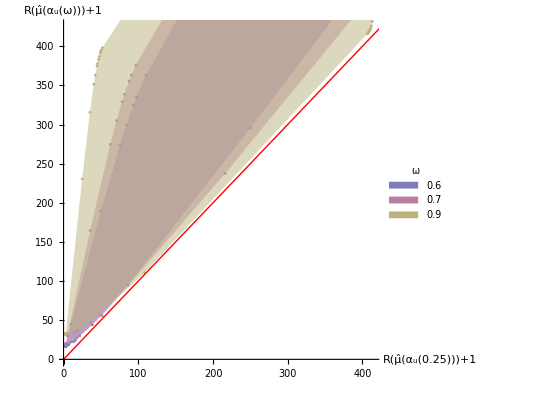

```mathematica
figureY=drawFeasibleSets[
fYData[[{11,12,13}]],
{"ω",getOmega},
Diagonal->True,Bounds->True,
PlotRange->{All,{0,425}},
AxesLabel ->{universalName[0.25],universalName[ω]}
]
```

```mathematica
figureYLog=drawLogFeasibleSets[
fYData[[{1,2,3,4}]],
{"ω",getOmega},
RIDiagonal->True,Bounds->True,
PlotRange->{{1,400},{1,400}},
AxesLabel ->{universalName[0.25],universalName[ω]}
]
```

-Graphics-

```mathematica
Export["~/Desktop/figure.pdf",figureY]
Export["~/Desktop/figureLog.pdf",figureYLog]
```

### Figure Z Compare universal bidders with ω=0.25, different W_0

Make sure that the local machine destination directory path is valid.

```mathematica
initWealth = {0.05, 0.10,0.20,0.30,0.40,0.50}
id =With[
{scale=2,n=200},
Table[makeID[{.25,0,.25},{initWealth⟦j⟧,0,0.25},scale,n], {j,1,Length[initWealth]}]
]

fZData=Table[getData[id⟦i⟧,"Z","var:"],{i,1,Length[id]}]; 
{Length[fZData], Dimensions[fZData⟦1,3⟧]}
```

{0.05,0.1,0.2,0.3,0.4,0.5}

{{summary_risk_alpha25_00_25_beta05_00_25_scale2_n200,{{0.25,0,0.25},{0.05,0,0.25},2,200}},{summary_risk_alpha25_00_25_beta10_00_25_scale2_n200,{{0.25,0,0.25},{0.1,0,0.25},2,200}},{summary_risk_alpha25_00_25_beta20_00_25_scale2_n200,{{0.25,0,0.25},{0.2,0,0.25},2,200}},{summary_risk_alpha25_00_25_beta30_00_25_scale2_n200,{{0.25,0,0.25},{0.3,0,0.25},2,200}},{summary_risk_alpha25_00_25_beta40_00_25_scale2_n200,{{0.25,0,0.25},{0.4,0,0.25},2,200}},{summary_risk_alpha25_00_25_beta50_00_25_scale2_n200,{{0.25,0,0.25},{0.5,0,0.25},2,200}}}

{6,{37,6}}

```mathematica
fZData⟦1,3⟧//TableForm
```

#### Feasible sets

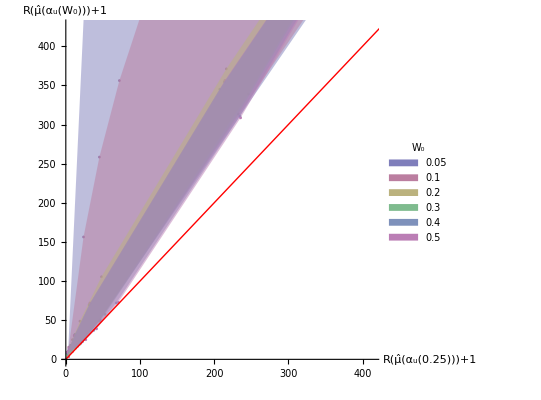

```mathematica
figureZ=drawFeasibleSets[
fZData,
{"W_0",getW0Beta},
Diagonal->True,Bounds->True,
PlotRange->{All,{0,425}},
AxesLabel ->{universalName[0.25],universalName[Subscript[W, 0]]}
]
```

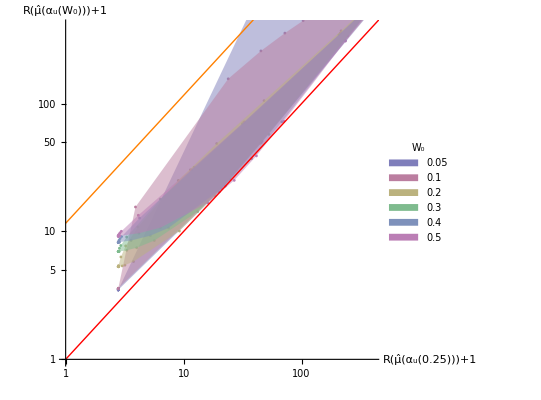

```mathematica
figureYLog=drawLogFeasibleSets[
fZData,
{"W_0",getW0Beta},
RIDiagonal->True,Bounds->True,
PlotRange->{{1,400},{1,400}},
AxesLabel ->{universalName[0.25],universalName[Subscript[W, 0]]}
]
```

```mathematica
Export["~/Desktop/figure.pdf",figureY]
Export["~/Desktop/figureLog.pdf",figureYLog]
```

### Additional Plots Risk Inflation, Effects of number of tests

This plot shows the feasible set in a log-log plot to zoom in on the growth trajectory.  Probably should not have that diagonal arrow returning to the left since the set is not convex on the log-log scale.

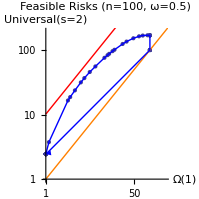
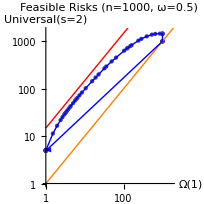
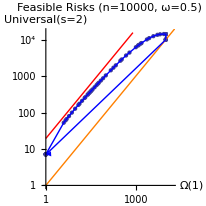
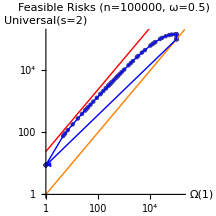

This is a plot to show the results for various values of n on the same graph. The align function rescales the oracle in the argument to match that in the reference set of coordinates.  Of course, all of the xy coordinate pairs (tables) need to be computed on the same grid.

```mathematica
(#⟦1⟧&/@xy[100])/(#⟦1⟧&/@xy[1000])xy[1000]
```

{{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1.,4.9781},{1.,7.46352},{1.,8.48179},{1.,9.09503},{1.,9.34627},{1.,9.54859},{1.,9.61351},{1.,9.6637},{1.,9.71541},{1.,9.76704},{1.,9.81115},{1.,9.83086},{1.,9.89444},{1.,9.92133},{1.,9.92079},{1.,9.91244},{1.,9.87986},{1.,9.81371},{1.14717,11.0705},{2.66802,24.7584},{2.94506,26.5979},{3.63303,31.9382},{4.72828,39.5592},{5.52181,45.2578},{7.02061,53.482},{9.00586,63.6606},{13.4679,82.3334},{15.4683,89.052},{16.5512,93.6673},{19.2555,102.521},{20.9676,108.264},{30.1292,129.591},{35.8269,140.711},{48.5095,156.406},{62.3546,161.448},{73.5121,160.915},{90.9595,152.964},{101.,145.346},{101,145.346},{101,145.346},{101,145.346},{101,145.346},{101,101.023},{101,101},{101,101},{101,101},{101,101},{101,101},{1.01568,4.95336},{1.00034,4.97694}}

```mathematica
Clear[ri];
ri[m_]:=With[
{ri=(#⟦2⟧/(2 Log[m] #⟦1⟧))& /@ (xy[m]),    (*  risk inflation as % of 2 log p *)
rpt=(#⟦1⟧/(2 Log[m]))& /@ (xy[m])                                               (* oracle risk per test *)
},
Sort[Transpose[{rpt,ri}],#1⟦1⟧≤#2⟦1⟧&]
]
```

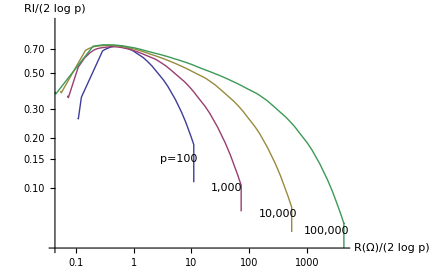

```mathematica
ListLogLogPlot[{ri[100],ri[1000],ri[10000],ri[100000]},
AxesLabel-> {"R(Ω)/(2 log p)","RI/(2 log p)"},
Epilog->{
Text["p=100",Log[{6,0.15}]],
Text["1,000",Log[{40,0.10}]],
Text["10,000",Log[{320,0.07}]],
Text["100,000",Log[{2150,0.055}]]},
Joined->True]
```